```mathematica
GetDistinctFactors[x_]:=Module[{f=FactorInteger[x],g={}},
l=Length[f];
For[i=1,i≤l,i++,
AppendTo[g,f[[i]][[1]]];];
Return[g]]
```

```mathematica
GetRepeatedFactors[x_]:=Module[{f=FactorInteger[x],g={}},
l=Length[f];
For[i=1,i≤l,i++,
For[j=1,j≤f[[i]][[2]],j++,
AppendTo[g,f[[i]][[1]]]]];
Return[g]]
```

```mathematica
Tgrf[x_]:=If[PrimeQ[x],0,Total[GetRepeatedFactors[x]]]
```

```mathematica
Ct[x_]:=Module[{c=0},
If[PrimeQ[x]||x<=4,Return[0]];
t=Tgrf[x];
While[True,
c+=1;
If[PrimeQ[t],Return[c]];
t=Tgrf[t];];]
```

```mathematica
A[n_]:=Select[Table[Ct[x],{x,n}],#>0&]
```

```mathematica
Tally[A[10^6]]
```

{{1,108572},{2,135858},{3,151258},{4,143889},{5,134497},{6,144425},{7,74494},{8,22640},{9,4991},{10,790},{11,80},{12,5},{13,1}}

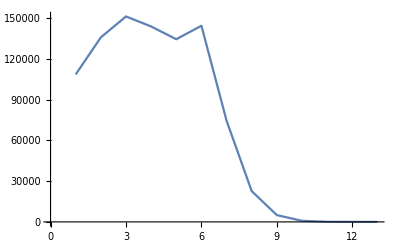

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
For[i=5,i<10^6,i++,If[Ct[i]==13,i]]
```

$Aborted